```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\definecolor{forestgreen}{rgb}{0.3,0.7,0}","\\definecolor{waterblue}{rgb}{0,0.3,0.7}","\\definecolor{orangemelon}{rgb}{1,0.7,0.3}","\\definecolor{shockpink}{rgb}{1,0.,0.7}"}]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color},\definecolor{forestgreen}{rgb}{0.3,0.7,0},\definecolor{waterblue}{rgb}{0,0.3,0.7},\definecolor{orangemelon}{rgb}{1,0.7,0.3},\definecolor{shockpink}{rgb}{1,0.,0.7}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(* Taking the non-linear power spectrum at different redshift *)
SetDirectory[StringJoin[NotebookDirectory[],"output"]];
zvec=Table[i,{i,0,12,0.1}];
pnlz={};
For[j=0,j<Length[zvec],j++;
fn1=ToString[j];
fn=StringJoin["powersp00_z",fn1,"_pk_nl.dat"];
pn=Import[fn][[5;;]];
pnlz=Join[pnlz,Table[{zvec[[j]],pn[[i,1]],pn[[i,2]]},{i,1,Length[pn]}]];
]
ClearAll[Pδnl]
Pδnlcdm=Interpolation[pnlz,InterpolationOrder->1];(* z, k in h/Mpc , in (Mpc/h)^3*)
(***)

(*** Warm power spectrum ***)
SetDirectory[StringJoin[NotebookDirectory[],"outputHDM_relic/outputHDM_m15"]];
zvec=Table[i,{i,0,12,0.1}];
pnlz={};
tkzncdm={};
tkzm={};
For[j=0,j<Length[zvec],j++;
fn1=ToString[j];
fn=StringJoin["powersp00_z",fn1,"_pk_nl.dat"];
pn=Import[fn][[5;;]];
pnlz=Join[pnlz,Table[{zvec[[j]],pn[[i,1]],pn[[i,2]]},{i,1,Length[pn]}]];

fn=StringJoin["powersp00_z",fn1,"_tk.dat"];
pn=Import[fn][[10;;]];
tkzncdm=Join[tkzncdm,Table[{zvec[[j]],pn[[i,1]],pn[[i,6]]},{i,1,Length[pn]}]];
tkzm=Join[tkzm,Table[{zvec[[j]],pn[[i,1]],pn[[i,4]]},{i,1,Length[pn]}]];
]
ClearAll[Pδnl15r,Pwdm15r]
Pδnl15r=Interpolation[pnlz,InterpolationOrder->1];(* z, k in h/Mpc , in (Mpc/h)^3*)
Tncdm15r=Interpolation[tkzncdm,InterpolationOrder->1];(* z, k in h/Mpc , in (Mpc/h)^3*)
Tcdm15r=Interpolation[tkzm,InterpolationOrder->1];(* z, k in h/Mpc , in (Mpc/h)^3*)
Pwdm15r[z_,k_]:=(Tncdm15r[z,k]/Tcdm15r[z,k])^2 Pδnl15r[z,k];
```

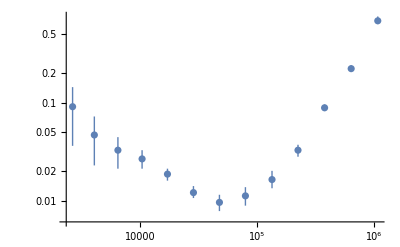

```mathematica
hst606={{2628.39,0.090.050.05},{4038.48,0.0470.0240.025},{6431.17,0.0330.0120.012},{10364.4,0.0270.0050.006},{17106.5,0.01870.00270.0025},{28573.2,0.01210.00150.0020},{47726.2,0.00960.00180.0019},{79717.6,0.01120.00230.0025},{134752.,0.01650.00300.004},{225077.,0.0330.0050.004},{380462.,0.0890.0070.007},{643117.,0.2230.0110.018},{1.0871*^6,0.680.050.07}};
ListPlot[hst606,ScalingFunctions->{"Log","Log"}]
```

```mathematica
(* Cosmological parameters *)
h=0.674;
ρc=1.053672*10^-5*h^2 *10^9(1.973*10^-5)^3; (*eV^4, critical density*)
kmstoMpc=10^5*0.334*10^-10;
H0=h 100kmstoMpc;(*1/Mpc*)
MpctoeV=10^6*3.08*10^18 1/(1.973*10^-5);
Ω0b=h^-2 0.02237;
Ω0cdm=h^-2 0.1200;
Ω0r=5.38*10^-5;
Ω0m=0.315;
Ω0Λ=0.685;
H[z_?NumericQ]:=H0 √(Ω0m(1+z)^3+Ω0Λ+Ω0r(1+z)^4)1/MpctoeV;(*eV*)
r[z_?NumericQ]:=NIntegrate[1/H[zz],{zz,0,z}];(*in eV^-1*)
t[z_?NumericQ]:=NIntegrate[1/((1+zz)H[zz]),{zz,z,∞}];(*in eV^-1*)
(******)
```

```mathematica
z=1;

dx=1;
fulldiv=Sort[Flatten[Table[i*10^j,{i,2,9,dx},{j,-30,6}],1]];
spdiv=Sort[Flatten[Table[i*10^j,{i,1,1},{j,-30,6}],1]];
chardiv={"10^-30","10^-29","10^-28","10^-27","10^-26","10^-25","10^-24","10^-23","10^-22","10^-21","10^-20","10^-19","10^-18","10^-17","10^-16","10^-15","10^-14","10^-13","10^-12","10^-11","10^-10","10^-9","10^-8","10^-7","10^-6","10^-5","10^-4","10^-3","10^-2","10^-1","1","10","10^2","10^3","10^4","10^5","10^6"};

mindiv=Table[{fulldiv[[i]]," ",{0.01,0.},{Directive[Black,AbsoluteThickness[0.1]]}},{i,1,Length[fulldiv]}];
majdiv=Table[{spdiv[[i]],chardiv[[i]],{0.02,0.},{Directive[Black,AbsoluteThickness[0.1]]}},{i,1,Length[spdiv]}];
majdivno=Table[{spdiv[[i]]," ",{0.02,0.},{Directive[Black,AbsoluteThickness[0.1]]}},{i,1,Length[spdiv]}];
div=Join[majdiv,mindiv];
divno=Join[majdivno,mindiv];

Show[LogLogPlot[{Pδnlcdm[z,l/(h(r[z]/MpctoeV))],Pwdm15r[z,l/(h(r[z]/MpctoeV))]},{l,10^2,10^6},PlotStyle->{Black,{Black,Dashed}},Frame->True,GridLines->{{7*h(r[z]/MpctoeV)}},GridLinesStyle->Dashed,PlotRange->{{10^2,10^6},{10^-4,10^4}},
FrameLabel->{MaTeX["l",Magnification->1.4],MaTeX["P_\\delta\\,[h^{-3}\\,\\mathrm{Mpc}^{-3}]",Magnification->1.4]}(*FrameLabel -> {Style["m_a (eV)",Magnification->1.4, FontSize -> 20  (*, Bold*)], 
    Style["Γ (s^-1)", FontSize -> 20  (*, Bold*)]  }, *),
  FrameStyle -> Directive[Black, FontSize -> 15, FontFamily->"Latin Modern Roman"],
       AspectRatio -> 0.70, 
     FrameTicks->{{div,divno},{div,divno}}, ImageSize -> 500],Graphics[{Line[{{Log[1.5*10^2],Log[5*10^-2]},{Log[4*10^2],Log[5*10^-2]}}]}],Graphics[Inset[Rotate[MaTeX["\\text{CDM}",Magnification->1.4],0.],{Log[7.5*10^2],Log[5*10^-2]}]],
Graphics[{Dashed,Line[{{Log[1.5*10^2],Log[10^-2]},{Log[4*10^2],Log[10^-2]}}]}],Graphics[Inset[Rotate[MaTeX["\\text{Freeze-out}",Magnification->1.4],0.],{Log[1.1*10^3],Log[10^-2]}]],Graphics[{Dotted,Line[{{0.25,22},{0.65,22}}]}],
Graphics[{Dotted,Line[{{Log[1.5*10^2],Log[1.8*10^-3]},{Log[4*10^2],Log[1.8*10^-3]}}]}],Graphics[Inset[Rotate[MaTeX["\\text{Hot relic}",Magnification->1.4],0.],{Log[0.97*10^3],Log[1.8*10^-3]}]],Graphics[{Dotted,Line[{{0.25,22},{0.65,22}}]}],Graphics[Inset[Rotate[MaTeX["m_a=10\\,\\mathrm{eV}",Magnification->1.4],0.],{Log[2.2*10^5],Log[10^3]}]],Graphics[Inset[Rotate[MaTeX["\\color{red}{m_a=15\\,\\mathrm{eV}}",Magnification->1.4],0.],{Log[2.2*10^5],Log[2*10^2]}]]]
```

-Graphics-

```mathematica
(* Characterizing the throughput *)
Clear[eff]
emin=1.7;(*eV*)
emax=2.6;(*eV*)
ϵ=0.3;(*efficiency*)
norm=ϵ(emax-emin);
eff[x_]:=1/norm Piecewise[{{0,x<emin},{ϵ,emin<x<emax},{0,x>emax}}];

ϵ=0.1;
ma=10;(*eV*)
gag=10^-11;(*eV*)
Γ[gag_,ma_]:=gag^2 ma^3/(64π)1/10^18 1.519*10^15;(*s^-1*)
dNdEdt[ω_,z_]:=2Γ[gag,ma] 1/(√(2π ϵ))E^((-(ω(1+z)-ma/2)^2)/(2ϵ));(*like δ(ω(1+z)-ma/2), s^-1 eV^-1*)
(*
Cl[l_,ωpiv_]:=NIntegrate[1/r[z]^2 1/H[z](ωpiv^2/(4π)(Ω0cdm ρc)/ma NIntegrate[eff[ω]/ω dNdEdt[ω,z],{ω,emin,emax}])^2 Pδnlcdm[z,l/(h(r[z]/MpctoeV))],{z,10^-3,11.9}](1.6022*10^-19*10^9)^2(0.507*10^5 1/10^-2)^4(MpctoeV/h)^3;(*in (nW/(m^2 sr))^2*)

*)
Cl[l_,ωpiv_]:=NIntegrate[1/r[z]^2 1/H[z](ωpiv^2/(4π)(Ω0cdm ρc)/ma dNdEdt[ωpiv,z])^2 Pδnlcdm[z,l/(h(r[z]/MpctoeV))],{z,10^-3,11.9}](1.6022*10^-19*10^9)^2(0.507*10^5 1/10^-2)^4(MpctoeV/h)^3;(*in (nW/(m^2 sr))^2*)
```

```mathematica
ωpiv=(2π)/(606*10^-7)1.973*10^-5(*eV*);
Monitor[tt=Table[{hst606[[i,1]],hst606[[i,1]]^2/(2π)(Cl[hst606[[i,1]],ωpiv])},{i,1,Length[hst606]}],i];
Show[ListLogLogPlot[{hst606,tt},Frame->True,PlotRange->{{10^2,2*10^6},{10^-3.5,10}},Joined->{False,True},PlotStyle->{Black,{Directive[Thickness[4*10^-3],Black]},{Dashed,Black}},FrameLabel->{MaTeX["l",Magnification->1.4],MaTeX["\\frac{l^2}{2\\,\\pi}\\,C_l\\,[\\mathrm{nW}^2\\,\\mathrm{m}^{-4}\\,\\mathrm{sr}^{-2}]",Magnification->1.4]}(*FrameLabel -> {Style["m_a (eV)",Magnification->1.4, FontSize -> 20  (*, Bold*)], 
    Style["Γ (s^-1)", FontSize -> 20  (*, Bold*)]  }, *),
  FrameStyle -> Directive[Black, FontSize -> 15, FontFamily->"Latin Modern Roman"],
       AspectRatio -> 0.70, 
     FrameTicks->{{div,divno},{div,divno}}, ImageSize -> 500],Graphics[Inset[Rotate[MaTeX[" C_l^{\\mathrm{obs}} \\, \\mathrm{HST}\\,606\\,\\mathrm{nm}",Magnification->1.4],0.],{Log[3.2*10^5],Log[4]}]],
Graphics[{Directive[Thickness[4*10^-3],Black],Line[{{Log[2*10^2],Log[4]},{Log[5*10^2],Log[4]}}]}],Graphics[Inset[Rotate[MaTeX["\\text{CDM}",Magnification->1.4],0.],{Log[1.05*10^3],Log[4]}]]]
```

-Graphics-

```mathematica
(*PBH, 2212.11977.pdf*)
gi=2;
MPBH=10^23;(*g*)
MPBHineV=MPBH*0.561*10^33;(*eV*)
rPBH=2 MPBHineV/((1.22*10^19*10^9)^2);(*eV^-1*)
σs=27π rPBH^2;
TPBH=((1.22*10^19*10^9)^2)/MPBHineV;(*eV*)

dNdEdt[ω_,z_]:=σs gi/(2π)(ω(1+z))^2/(E^(ω(1+z)/TPBH)-1)1/(0.658*10^-15);(*like δ(ω(1+z)-ma/2), s^-1 eV^-1*)


Cl[l_,ωpiv_]:=NIntegrate[1/r[z]^2 1/H[z](ωpiv^2/(4π)(Ω0cdm ρc)/MPBHineV dNdEdt[ωpiv,z])^2 Pδnlcdm[z,l/(h(r[z]/MpctoeV))],{z,10^-3,11.9}](1.6022*10^-19*10^9)^2(0.507*10^5 1/10^-2)^4(MpctoeV/h)^3;(*in (nW/(m^2 sr))^2*)
```

```mathematica
ωpiv=(2π)/(606*10^-7)1.973*10^-5(*eV*);
Monitor[tt=Table[{hst606[[i,1]],hst606[[i,1]]^2/(2π)(Cl[hst606[[i,1]],ωpiv])},{i,1,Length[hst606]}],i];
Show[ListLogLogPlot[{hst606,tt},Frame->True,PlotRange->{{10^2,2*10^6},{10^-3.5,10}},Joined->{False,True},PlotStyle->{Black,{Directive[Thickness[4*10^-3],Black]},{Dashed,Black}},FrameLabel->{MaTeX["l",Magnification->1.4],MaTeX["\\frac{l^2}{2\,\pi}\,C_l\,[\mathrm{nW}^2\,\mathrm{m}^{-4}\,\mathrm{sr}^{-2}]",Magnification->1.4]},
  FrameStyle -> Directive[Black, FontSize -> 15, FontFamily->"Latin Modern Roman"],
       AspectRatio -> 0.70, 
     FrameTicks->{{div,divno},{div,divno}}, ImageSize -> 500],Graphics[Inset[Rotate[MaTeX[" C_l^{\mathrm{obs}} \, \mathrm{HST}\,606\,\mathrm{nm}",Magnification->1.4],0.],{Log[3.2*10^5],Log[4]}]],
Graphics[{Directive[Thickness[4*10^-3],Black],Line[{{Log[2*10^2],Log[4]},{Log[5*10^2],Log[4]}}]}],Graphics[Inset[Rotate[MaTeX["\\text{CDM}",Magnification->1.4],0.],{Log[1.05*10^3],Log[4]}]]]
```

-Graphics-